```mathematica
(*Denominator 1st term*)
```

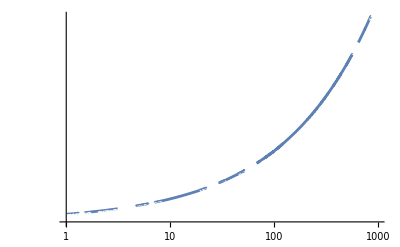

```mathematica
ω=2*Pi*f;
deno1re=(s*E0*k2*Cos[k2*L]-M*ω^2*Sin[k2*L])*(ρ*ω^2 /E0/s*Sin[kd*L]*Cosh[kd*L]-ω/χ*Cos[kd*L]*Sinh[kd*L])/.
kd->Sqrt[ω/2/χ]/.χ->κ/ρ/Cv/.k2->Sqrt[ρ*ω^2/E0/s]/.
{ρ->0.008,κ->0.00008,Cv->790,E0->4*10^{11} (*Young's modulus*),L->0.35,s->0.0016^2*Pi/4,M->22.8/4};(**)
LogLogPlot[deno1re,{f,1,1000}]
```

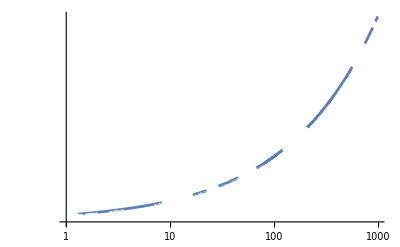

```mathematica
deno1im=ω/χ*Sin[kd*L]*Cosh[kd*L]+ρ*ω^2 /E0/s*Cos[kd*L]*Sinh[kd*L]/.
kd->Sqrt[ω/2/χ]/.χ->κ/ρ/Cv/.
{ρ->0.008,κ->0.00008,Cv->790,E0->4*10^{11} (*Young's modulus*),L->0.35,s->0.0016^2*Pi/4,χ->1.27*10^{-5}};(*χ->κ/ρ/Cv*)
LogLogPlot[deno1im,{f,1,1000}]
```

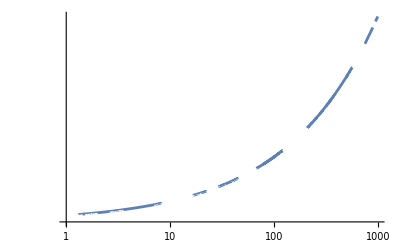

```mathematica
ω=2*Pi*f;
SCh=Sin[kd*L]*Cosh[kd*L]/.kd->Sqrt[ω/2/χ]/.χ->κ/ρ/Cv/.
{ρ->0.008,κ->0.00008,Cv->790,E0->4*10^{11} (*Young's modulus*),L->0.35,s->0.0016^2*Pi/4,χ->1.27*10^{-5}};
LogLogPlot[SCh,{f,1,1000}]
```

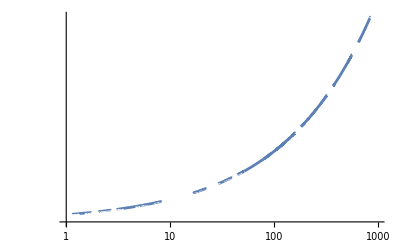

```mathematica
(*denomenator 2nd term*)

ω=2*Pi*f;
minusDeno2re=kd*(Cos[kd*L]*Cosh[kd*L]+Sin[kd*L]*Sinh[kd*L])+(χ*ρ* ω)/(s*E0)*(Cos[kd*L]*Cosh[kd*L]-Sin[kd*L]*Sinh[kd*L])/.
kd->Sqrt[ω/2/χ]/.χ->κ/ρ/Cv/.
{ρ->0.008,κ->0.00008,Cv->790,E0->4*10^{11} (*Young's modulus*),L->0.35,s->0.0016^2*Pi/4,χ->1.27*10^{-5}};
LogLogPlot[minusDeno2re,{f,1,1000}]
```

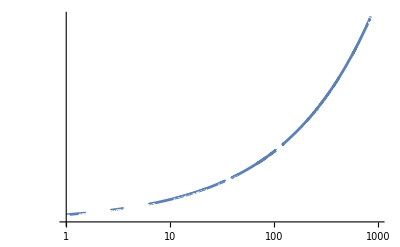

```mathematica
ω=2*Pi*f;
Deno2im=kd*(Cos[kd*L]*Cosh[kd*L]-Sin[kd*L]*Sinh[kd*L])-(χ*ρ* ω)/(s*E0)*(Cos[kd*L]*Cosh[kd*L]+Sin[kd*L]*Sinh[kd*L])/.
kd->Sqrt[ω/2/χ]/.χ->κ/ρ/Cv/.
{ρ->0.008,κ->0.00008,Cv->790,E0->4*10^{11} (*Young's modulus*),L->0.35,s->0.0016^2*Pi/4,χ->1.27*10^{-5}};
LogLogPlot[Deno2im,{f,1,1000}]
```